```mathematica
(*Воложинец Архип гр.221703
  ПЗ №3
  Вариант 3*)
```

```mathematica
(*1 Задание*)
```

```mathematica
f[x_] := √(x^3+4)*Cos[x/(√17)+1/21]
```

```mathematica
(*n = 6*)
```

```mathematica
n = 6
```

6

```mathematica
a =0
b = 6
h = b/n
```

0

6

1

```mathematica
Data=N[Table[{i h,f[i h]},{i,0,n}]];
```

```mathematica
TableForm[Data]
```

0. | 1.99773
1. | 2.1426
2. | 2.98413
3. | 3.97685
4. | 4.3315
5. | 3.4702
6. | 1.00729

```mathematica
DataX=Table[Data⟦i,1⟧,{i,n+1}];
DataY=Table[Data⟦i,2⟧,{i,n+1}];
```

```mathematica
(*1.a)*)
```

```mathematica
LagrangeInterpolation[DataX_,DataY_,n_]:=∑_(i=1)^n DataY[[i]]*Product[If[i!=j,(x-DataX[[j]])/(DataX[[i]]-DataX[[j]]),1],{j,1,Length[DataX]}];
```

```mathematica
Ln=LagrangeInterpolation[Data[[All,1]],Data[[All,2]],n+1]//Simplify
```

1.99773-0.154283 x+0.139234 x^2+0.250972 x^3-0.104069 x^4+0.0136724 x^5-0.000658642 x^6

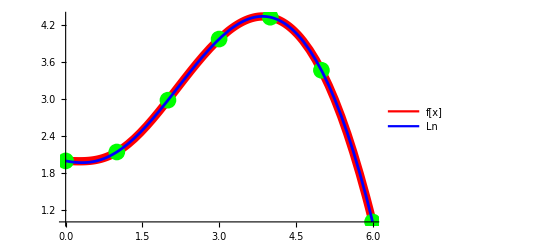

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Ln,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Ln"}]]
```

```mathematica
(*1.б)*)
```

```mathematica
Array[difference,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,difference[i,k]=""]];
For[i=0,i<=n,i++,difference[i,0]=Data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
difference[i,k]=difference[i+1,k-1]-difference[i,k-1]]];
table=Array[difference,{n+1,n+1},{0,0}];
TableForm[table]
```

1.99773 | 0.144867 | 0.696663 | -0.545474 | -0.243776 | 0.455127 | -0.474222
2.1426 | 0.84153 | 0.151189 | -0.789251 | 0.211351 | -0.0190955 | 
2.98413 | 0.992718 | -0.638062 | -0.5779 | 0.192255 |  | 
3.97685 | 0.354657 | -1.21596 | -0.385645 |  |  | 
4.3315 | -0.861306 | -1.60161 |  |  |  | 
3.4702 | -2.46291 |  |  |  |  | 
1.00729 |  |  |  |  |  |

```mathematica
(*1.в)*)
```

```mathematica
findNewtonInter[DataX_,DataY_,deltaTable_,h_,n_]:=DataY[[n]]+∑_(i=1)^(n-1) ((∏_(k=1)^i ((x-DataX[[n]])/h+k-1))/Factorial[i]*deltaTable[[n-i,i+1]]);
Pn=findNewtonInter[DataX,DataY,table,h,n+1]//Simplify
```

1.99773-0.154283 x+0.139234 x^2+0.250972 x^3-0.104069 x^4+0.0136724 x^5-0.000658642 x^6

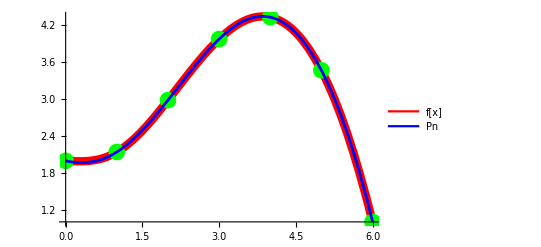

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Pn,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Pn"}]]
```

```mathematica
(*1.г)*)
```

```mathematica
Np=InterpolatingPolynomial[Data,x];
Np=Simplify[Np]
```

1.99773-0.154283 x+0.139234 x^2+0.250972 x^3-0.104069 x^4+0.0136724 x^5-0.000658642 x^6

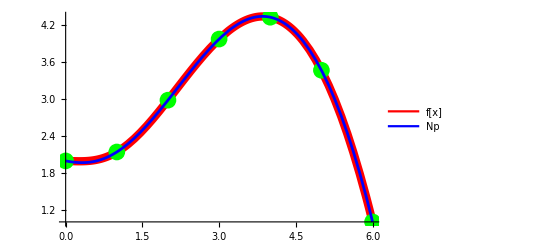

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Np,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Np"}]]
```

```mathematica
(*1.д)*)
```

```mathematica
f[2.4316]
Ln/.x->2.4316
Pn/.x->2.4316
Np/.x->2.4316
```

3.44521

3.44199

3.44199

3.44199

```mathematica
(*1.е)*)
```

```mathematica
Rn=Abs[f[x]-Np];
```

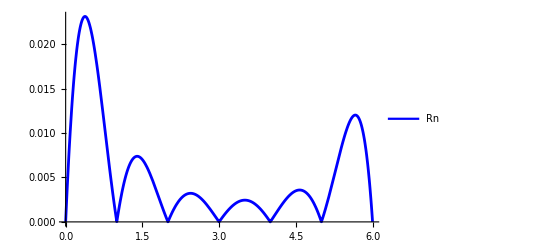

```mathematica
graph1=Plot[Rn,{x,0,6},PlotStyle->Blue];
Legended[Show[graph1],LineLegend[{Blue},{"Rn"}]]
```

```mathematica
Maximize[{Rn,a<=x<=b},x]
```

{0.0231125,{x→0.378675}}

```mathematica
(*n = 10*)
```

```mathematica
n=10;
h=b/n;
Data=N[Table[{i h,f[i h]},{i,0,n}]];
TableForm[Data]
```

0. | 1.99773
0.6 | 2.01511
1.2 | 2.25738
1.8 | 2.77518
2.4 | 3.4121
3. | 3.97685
3.6 | 4.30757
4.2 | 4.27163
4.8 | 3.76106
5.4 | 2.69216
6. | 1.00729

```mathematica
DataX=Table[Data[[i,1]],{i,n+1}];
DataY=Table[Data[[i,2]],{i,n+1}];
```

```mathematica
(*1.a)*)
```

```mathematica
Ln=LagrangeInterpolation[DataX,DataY,n+1]//Simplify
```

1.99773+0.0185194 x-0.215355 x^2+0.434111 x^3-0.0308856 x^4-0.105746 x^5+0.0561184 x^6-0.0142151 x^7+0.00202536 x^8-0.000156039 x^9+5.07631×10^-6 x^10

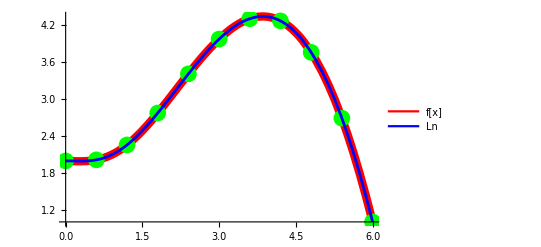

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Ln,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Ln"}]]
```

```mathematica
(*1.б)*)
```

```mathematica
Array[difference,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,difference[i,k]=""]];
For[i=0,i<=n,i++,difference[i,0]=Data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
difference[i,k]=difference[i+1,k-1]-difference[i,k-1]]];
table=Array[difference,{n+1,n+1},{0,0}];
TableForm[table]
```

1.99773 | 0.0173789 | 0.224893 | 0.0506338 | -0.207036 | 0.172136 | -0.107773 | 0.0431372 | 0.0172774 | -0.0694057 | 0.111384
2.01511 | 0.242272 | 0.275527 | -0.156402 | -0.0349001 | 0.0643626 | -0.0646362 | 0.0604147 | -0.0521282 | 0.0419785 | 
2.25738 | 0.517798 | 0.119124 | -0.191303 | 0.0294625 | -0.0002736 | -0.00422159 | 0.00828641 | -0.0101498 |  | 
2.77518 | 0.636922 | -0.0721786 | -0.16184 | 0.0291889 | -0.00449519 | 0.00406482 | -0.00186335 |  |  | 
3.4121 | 0.564744 | -0.234019 | -0.132651 | 0.0246937 | -0.000430374 | 0.00220146 |  |  |  | 
3.97685 | 0.330725 | -0.36667 | -0.107958 | 0.0242633 | 0.00177109 |  |  |  |  | 
4.30757 | -0.0359449 | -0.474627 | -0.0836942 | 0.0260344 |  |  |  |  |  | 
4.27163 | -0.510572 | -0.558322 | -0.0576598 |  |  |  |  |  |  | 
3.76106 | -1.06889 | -0.615981 |  |  |  |  |  |  |  | 
2.69216 | -1.68488 |  |  |  |  |  |  |  |  | 
1.00729 |  |  |  |  |  |  |  |  |  |

```mathematica
(*1.в)*)
```

```mathematica
Pn=findNewtonInter[DataX,DataY,table,h,n+1]//Simplify
```

1.99773+0.0185194 x-0.215355 x^2+0.434111 x^3-0.0308856 x^4-0.105746 x^5+0.0561184 x^6-0.0142151 x^7+0.00202536 x^8-0.000156039 x^9+5.07631×10^-6 x^10

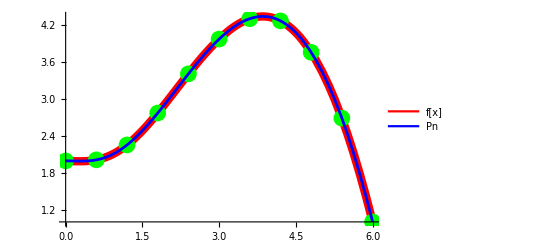

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Pn,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Pn"}]]
```

```mathematica
(*1.д)*)
```

```mathematica
Np=InterpolatingPolynomial[Data,x];
Np=Simplify[Np]
```

1.99773+0.0185194 x-0.215355 x^2+0.434111 x^3-0.0308856 x^4-0.105746 x^5+0.0561184 x^6-0.0142151 x^7+0.00202536 x^8-0.000156039 x^9+5.07631×10^-6 x^10

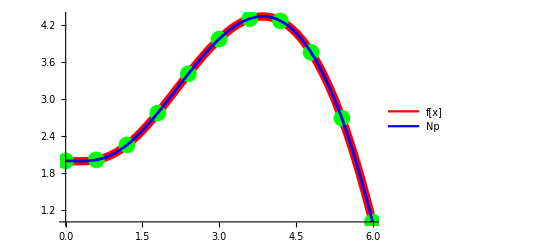

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Np,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Np"}]]
```

```mathematica
(*1.д)*)
```

```mathematica
f[2.4316]
Ln/.x->2.4316
Pn/.x->2.4316
Np/.x->2.4316
```

3.44521

3.44522

3.44522

3.44522

```mathematica
(*1.е)*)
```

```mathematica
Rn=Abs[f[x]-Np];
```

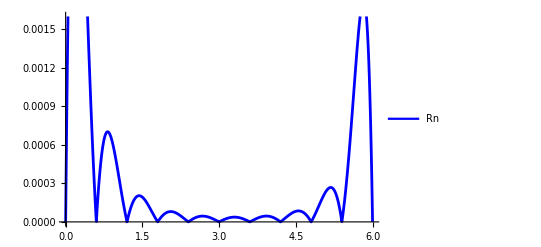

```mathematica
graph1=Plot[Rn,{x,0,6},PlotStyle->Blue];
Legended[Show[graph1],LineLegend[{Blue},{"Rn"}]]
```

```mathematica
Maximize[{Rn,a<=x<=b},x]
```

{0.00345993,{x→0.195904}}

```mathematica
(*1.ж)Вывод: При увеличении узлов интерполяции погрешность уменьшается.*)
```

```mathematica
(*2 Задание *)
(*n = 6*)
```

```mathematica
n=6;
```

```mathematica
For[i=0,i<=n,i++,Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(a+b)/2+(b-a)/2*Subscript[t, i];]
```

```mathematica
Data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
DataX=Table[Data[[i,1]],{i,n+1}];
DataY=Table[Data[[i,2]],{i,n+1}];
TableForm[Data]
```

5.92478 | 1.25356
5.34549 | 2.81403
4.30165 | 4.22113
3. | 3.97685
1.69835 | 2.67361
0.654506 | 2.02501
0.0752163 | 1.99577

```mathematica
(*2.а)*)
```

```mathematica
findDivividedDifferenceFunction[DataX_,DataY_,first_,last_]:=If[first+1==last,(DataY[[last]]-DataY[[first]])/(DataX[[last]]-DataX[[first]]),(findDivividedDifferenceFunction[DataX,DataY,first+1,last]-findDivividedDifferenceFunction[DataX,DataY,first,last-1])/(DataX[[last]]-DataX[[first]])]
```

```mathematica
Array[difference,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,difference[i,k]=""]];
For[i=0,i<=n,i++,difference[i,0]=Data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
difference[i,k]=findDivividedDifferenceFunction[DataX,DataY,i+1,k+i+1]]];
table=Array[difference,{n+1,n+1},{0,0}];
TableForm[table]
```

1.25356 | -2.69376 | -0.829117 | -0.059624 | 0.00809409 | 0.0000692167 | -0.000739371
2.81403 | -1.348 | -0.65473 | -0.0938331 | 0.0077293 | 0.00439422 | 
4.22113 | 0.187669 | -0.312507 | -0.130091 | -0.0154294 |  | 
3.97685 | 1.00122 | 0.161955 | -0.0648797 |  |  | 
2.67361 | 0.621356 | 0.351714 |  |  |  | 
2.02501 | 0.050478 |  |  |  |  | 
1.99577 |  |  |  |  |  |

```mathematica
differenceResult=Table[difference[i,k],{i,0,n},{k,1,n}];
```

```mathematica
(*2.б)*)
```

```mathematica
findNewtonDividedDifferenceFunction[DataX_,DataY_,n_,diff_]:=DataY[[1]]+∑_(i=1)^n diff[[1,i]]*∏_(k=1)^i (x-DataX[[k]])
```

```mathematica
Pnr=findNewtonDividedDifferenceFunction[DataX,DataY,n,differenceResult]//Simplify
```

2.00184-0.0841559 x+0.0234692 x^2+0.3155 x^3-0.120241 x^4+0.0155404 x^5-0.000739371 x^6

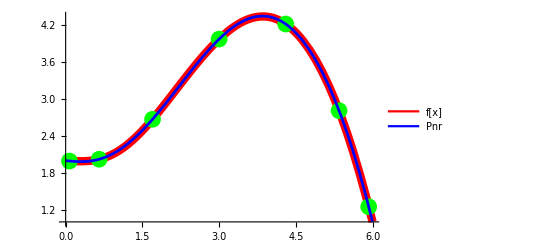

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Pnr,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Pnr"}]]
```

```mathematica
(*2.в)*)
```

```mathematica
Intf=Interpolation[Data];
```

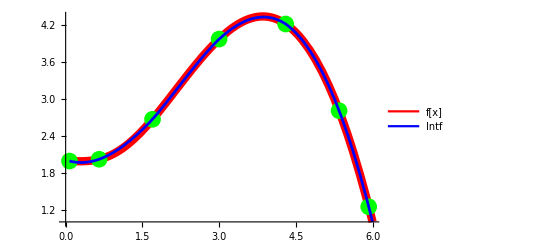

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Intf[x],{x,DataX[[n+1]],b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Intf"}]]
```

```mathematica
(*2.г)*)
```

```mathematica
f[2.4316]
Pnr/.x->2.4316
Intf[2.4316]
```

3.44521

3.43661

3.43661

```mathematica
(*2.д)*)
```

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
Maximize[{AbsPnr[x],a<=x<=b},x]
```

{0.00967787,{x→1.15209}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
Maximize[{AbsIntf[x],DataX[[n+1]]<=x<=DataX[[1]]},x]
```

{0.0308731,{x→1.1767}}

```mathematica
(*n = 10*)
```

```mathematica
n=10;
```

```mathematica
For[i=0,i<=n,i++,Subscript[t, i]=Cos[(Pi*(2*i+1))/(2*n+2)];Subscript[x, i]=(a+b)/2+(b-a)/2*Subscript[t, i]]
```

```mathematica
Data=N[Table[{Subscript[x, i],f[Subscript[x, i]]},{i,0,n}]];
DataX=Table[Data[[i,1]],{i,n+1}];
DataY=Table[Data[[i,2]],{i,n+1}];
TableForm[Data]
```

5.96946 | 1.10849
5.7289 | 1.84742
5.26725 | 2.98013
4.62192 | 3.96756
3.8452 | 4.34385
3. | 3.97685
2.1548 | 3.15021
1.37808 | 2.3871
0.732751 | 2.04306
0.271104 | 1.9921
0.0305357 | 1.99698

```mathematica
(*2.а)*)
```

```mathematica
Array[difference,{n+1,n+1},{0,0}];
For[k=1,k<=n,k++,
	For[i=n,i>=n-k,i--,difference[i,k]=""]];
For[i=0,i<=n,i++,difference[i,0]=Data[[i+1,2]]];
For[k=1,k<=n,k++,
For[i=0,i<=n-k,i++,
difference[i,k]=findDivividedDifferenceFunction[DataX,DataY,i+1,k+i+1]]];
table=Array[difference,{n+1,n+1},{0,0}];
TableForm[table]
```

1.10849 | -3.07159 | -0.880026 | -0.0339695 | 0.00873133 | 0.000227517 | 0.0000504621 | -8.17152×10^-6 | -0.0000201249 | 6.14019×10^-6 | 6.64259×10^-6
1.84742 | -2.45362 | -0.834251 | -0.0525172 | 0.00805573 | 0.0000350208 | 0.0000879807 | 0.0000972166 | -0.0000551139 | -0.0000333097 | 
2.98013 | -1.53013 | -0.735325 | -0.0745004 | 0.00793056 | -0.000347767 | -0.000397728 | 0.000398017 | 0.000134697 |  | 
3.96756 | -0.484458 | -0.566414 | -0.0991839 | 0.00928308 | 0.00145573 | -0.00238628 | -0.000307352 |  |  | 
4.34385 | 0.43422 | -0.321715 | -0.129297 | 0.00362151 | 0.011838 | -0.000975108 |  |  |  | 
3.97685 | 0.978046 | -0.00272437 | -0.140569 | -0.0386886 | 0.0155577 |  |  |  |  | 
3.15021 | 0.982465 | 0.315979 | -0.0349915 | -0.0848866 |  |  |  |  |  | 
2.3871 | 0.533126 | 0.381893 | 0.14533 |  |  |  |  |  |  | 
2.04306 | 0.110381 | 0.186054 |  |  |  |  |  |  |  | 
1.9921 | -0.0202695 |  |  |  |  |  |  |  |  | 
1.99698 |  |  |  |  |  |  |  |  |  |

```mathematica
differenceResult=Table[difference[i,k],{i,0,n},{k,1,n}];
```

```mathematica
(*2.б)*)
```

```mathematica
Pnr=findNewtonDividedDifferenceFunction[DataX,DataY,n,differenceResult]//Simplify
```

1.99777-0.024875 x-0.0365212 x^2+0.145948 x^3+0.213497 x^4-0.228116 x^5+0.0941137 x^6-0.0215967 x^7+0.00289609 x^8-0.000212863 x^9+6.64259×10^-6 x^10

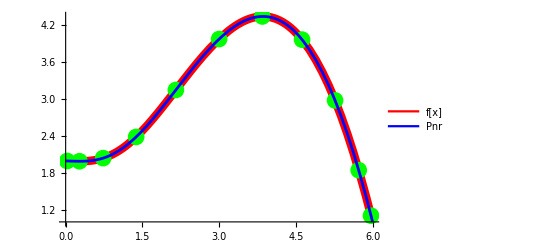

```mathematica
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Pnr,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Pnr"}]]
```

```mathematica
(*2.в)*)
```

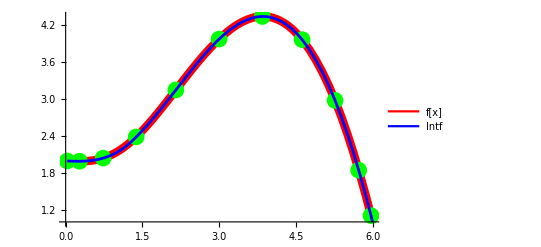

```mathematica
Intf=Interpolation[Data];
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Intf[x],{x,DataX[[n+1]],b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Intf"}]]
```

```mathematica
(*2.г)*)
```

```mathematica
f[2.4316]
Pnr/.x->2.4316
Intf[2.4316]
```

3.44521

3.44556

3.44279

```mathematica
(*2.д)*)
```

```mathematica
AbsPnr[x_]:=Abs[f[x]-Pnr];
Maximize[{AbsPnr[x],a<=x<=b},x]
```

{0.000424027,{x→1.75748}}

```mathematica
AbsIntf[x_]:=Abs[f[x]-Intf[x]];
Maximize[{AbsIntf[x],DataX[[n+1]]<=x<=DataX[[1]]},x]
```

{0.00849155,{x→1.15493}}

```mathematica
(*3 Задание*)
```

```mathematica
(*Исходя из выполнения вышеперчисленных действий, можно заметить, что чем больше количетсво точек интерполирования, тем меньше погрешность. Также величина погрешности зависит от положения точек на графике*)
```

```mathematica
(*4 Задание*)
```

```mathematica
n=10;
h=b/n;
Data=N[Table[{i h,f[i h]},{i,0,n}]];
TableForm[Data]
```

0. | 1.99773
0.6 | 2.01511
1.2 | 2.25738
1.8 | 2.77518
2.4 | 3.4121
3. | 3.97685
3.6 | 4.30757
4.2 | 4.27163
4.8 | 3.76106
5.4 | 2.69216
6. | 1.00729

```mathematica
(*4.а)*)
```

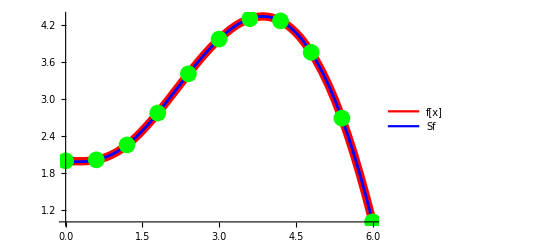

```mathematica
Sf=Interpolation[Data,Method->"Spline"];
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Sf[x],{x,DataX[[n+1]],b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,graph2,dotsGraph],LineLegend[{Red,Blue},{"f[x]","Sf"}]]
```

```mathematica
(*4.б)*)
```

```mathematica
f[2.4316]
Sf[2.4316]
```

3.44521

3.44519

```mathematica
(*5 Задание*)
```

```mathematica
n=10;
b=6;
h=b/n;
m=1;
Data=N[Table[{i h,f[i h]},{i,0,n}]];
DataX=Table[Data[[i,1]],{i,n+1}];
DataY=Table[Data[[i,2]],{i,n+1}];
TableForm[Data]
```

0. | 1.99773
0.6 | 2.01511
1.2 | 2.25738
1.8 | 2.77518
2.4 | 3.4121
3. | 3.97685
3.6 | 4.30757
4.2 | 4.27163
4.8 | 3.76106
5.4 | 2.69216
6. | 1.00729

```mathematica
(*5.а)*)
```

2.6724+0.0932628 x

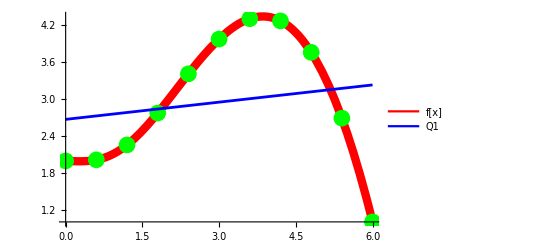

```mathematica
res=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) DataX[[j]]^(i+k)],{i,0,1}],{k,0,1}],Table[If[i==0,∑_(j=1)^(n+1) DataY[[j]],∑_(j=1)^(n+1) (DataY[[j]]*DataX[[j]]^i)],{i,0,1}]];
polRes=0;
For[i=0,i<=m,i++,polRes=polRes+res[[i+1]]*x^i];
Q1=polRes
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Q1,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Q1"}]]
```

```mathematica
(*5.б)*)
```

1.19992+1.72935 x-0.272682 x^2

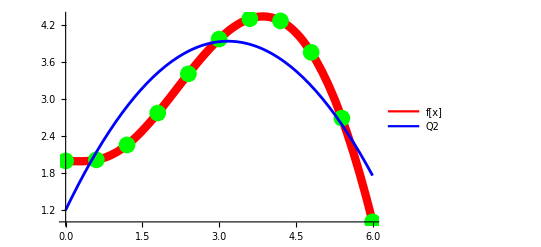

```mathematica
res=LinearSolve[Table[Table[If[i+k==0,∑_(j=1)^(n+1) 1,∑_(j=1)^(n+1) DataX[[j]]^(i+k)],{i,0,2}],{k,0,2}],Table[If[i==0,∑_(j=1)^(n+1) DataY[[j]],∑_(j=1)^(n+1) (DataY[[j]]*DataX[[j]]^i)],{i,0,2}]];
polRes=0;
For[i=0,i<=2,i++,polRes=polRes+res[[i+1]]*x^i];
Q2=polRes
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Q2,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Q2"}]]
```

```mathematica
(*5.в)*)
```

1.9958-0.378264 x+0.648479 x^2-0.102351 x^3

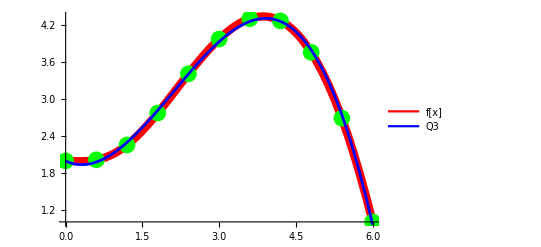

```mathematica
Q3=Fit[Data,{1,x,x^2,x^3},x]
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Q3,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Q3"}]]
```

2.02452-0.544448 x+0.786966 x^2-0.139281 x^3+0.00307748 x^4

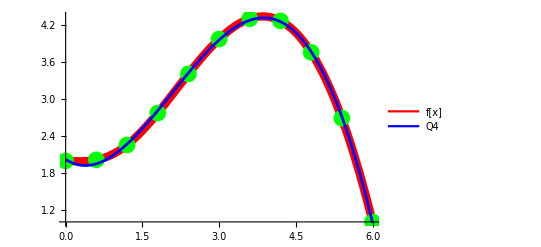

```mathematica
Q4=Fit[Data,{1,x,x^2,x^3,x^4},x]
graph1=Plot[f[x],{x,a,b},PlotStyle->{Red,Thickness[0.015]}];
graph2=Plot[Q4,{x,a,b},PlotStyle->Blue];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Green}];
Legended[Show[graph1,dotsGraph,graph2],LineLegend[{Red,Blue},{"f[x]","Q4"}]]
```

```mathematica
(*5.г)*)
```

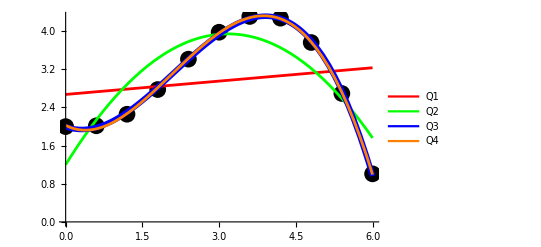

```mathematica
graph1=Plot[Q1,{x,a,b},PlotStyle->Red];
graph2=Plot[Q2,{x,a,b},PlotStyle->Green];
graph3=Plot[Q3,{x,a,b},PlotStyle->{Blue,Thickness[0.010]}];
graph4=Plot[Q4,{x,a,b},PlotStyle->Orange];
dotsGraph=ListPlot[Data,PlotStyle->{PointSize[0.03],Black}];
Legended[Show[dotsGraph,graph1,graph2,graph3,graph4],LineLegend[{Red,Green,Blue,Orange},{"Q1","Q2","Q3","Q4"}]]
```